## Projecto 2 HELP

## Cobweb ou Teia de Aranha

```mathematica
ClearAll[CobwebPlot]
SetAttributes[CobwebPlot,HoldAll]
CobwebPlot[f_,start_?NumericQ,n_,{xrange:{xmin_,xmax_},yrange:{_,_}}]:=Module[{cob,x,g1,coor},cob=NestList[f,start,n];
coor=Partition[Riffle[cob,cob],2,1];
coor[[1,2]]=0;
g1=Graphics[{Red,Line[coor]}];
Show[{Plot[{x,f[x]},{x,xmin,xmax},PlotStyle->{{Thick,Black},Blue},PlotRange->{xrange,yrange}],g1}]]
```

## Funcao de actualizacao da EDF

```mathematica
f[x_]:=2.8*(1-x)*x
```

Diagrama Cobweb (uma iteracao)

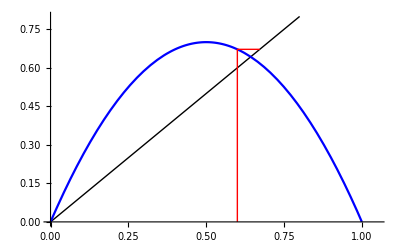

```mathematica
CobwebPlot[f,0.6,1,{{0,1.05},{0,0.8}}]
```

#### Diagrama Cobweb (cinco iteracoes)

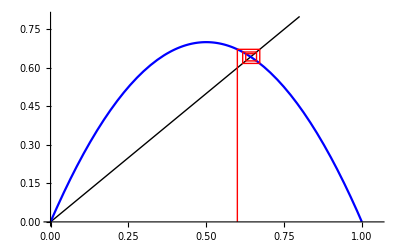

```mathematica
CobwebPlot[f,0.6,5,{{0,1.05},{0,0.8}}]
```

#### Zoom do diagrama (janela menor)

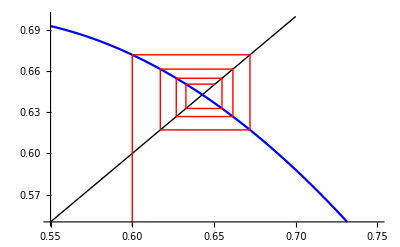

```mathematica
CobwebPlot[f,0.6,7,{{0.55,0.75},{0.55,0.7}}]
```

#### Novo zoom do diagrama (mais iteracoes, janela ainda menor)

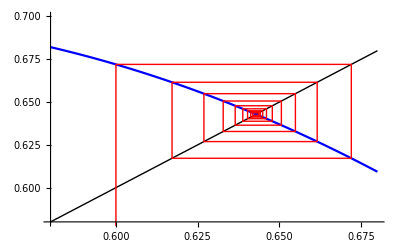

```mathematica
CobwebPlot[f,0.6,18,{{0.58,0.68},{0.58,0.7}}]
```

# RSOLVE

#### Caso em que resolve, sem condicao inicial

```mathematica
RSolve[a[n+1]==2*a[n]+3^n,a[n], n]
```

{{a[n]→-2^n+3^n+2^(-1+n) C[1]}}

#### Caso em que resolve, com condicao inicial

```mathematica
RSolve[{a[n+1]==2*a[n]+3^n,a[0]==0.5},a[n], n]
```

{{a[n]→-0.5 (1. 2^n-2. 3^n)}}

#### Caso em que não resolve, sem condicao inicial

```mathematica
RSolve[x[n+1]==1.25*Sin[x[n]],x[n],n]
```

RSolve[x[1+n]==1.25 Sin[x[n]],x[n],n]

#### Caso em que não resolve, com condicao inicial

```mathematica
RSolve[{x[n+1]==1.35*x[n]*Sin[x[n]],x[0]==1.4},x[n], n]
```

RSolve[{x[1+n]==1.35 Sin[x[n]] x[n],x[0]==1.4},x[n],n]

#### Obtemos 100 iteracoes sucessivas

```mathematica
R=RecurrenceTable[{x[n+1]==1.25*x[n]*Sin[x[n]],x[0]==2},x,{n,0,100}]
```

{2.,2.27324,2.16885,2.24051,2.1957,2.22595,2.20635,2.21943,2.21086,2.21655,2.2128,2.21528,2.21364,2.21473,2.21401,2.21449,2.21417,2.21438,2.21424,2.21433,2.21427,2.21431,2.21429,2.2143,2.21429,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143,2.2143}

#### Definimos funcao interpoladora das iteracoes

```mathematica
H=Interpolation[R]
```

InterpolatingFunction[{{1., 101.}}, <>]

#### Fazemos o grafico da funcao H

InterpolatingFunction::dmval: Input value {0.000449429} lies outside the range of data in the interpolating function. Extrapolation will be used.

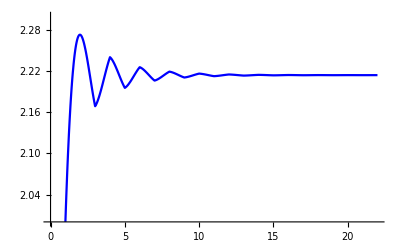

```mathematica
Plot[H[x],{x,0,22},PlotRange->{2,2.3},PlotStyle->{Blue}]
```